## Problem 1: Two Quantum Particles

## Problem 1(a)

```mathematica
ψ[x0_,x1_,x2_]:=1/Sqrt[Pi x0^2] ((x2-x1)/x0) Exp[-(x1^2+x2^2)/(2x0^2)]
pdf[x0_,x1_,x2_]:=FullSimplify@ComplexExpand@(ψ[x0,x1,x2]Conjugate[ψ[x0,x1,x2]])

Plot3D[pdf[1,x1,x2],{x1,-3,3},{x2,-3,3},PlotRange->Full,PlotTheme->"Classic",AxesLabel->{Subscript[x,1],Subscript[x,2],"|ψ|^2"},ImageSize->Large]
Export["/home/delon/Dropbox/notes/8.044/assignments/2_1.pdf",%];
```

-Graphics3D-

## Problem 1(b)

```mathematica
$Assumptions=Subscript[x,0]∈PositiveReals;
Integrate[pdf[Subscript[x,0],x,x2],{x2,-Infinity,Infinity}]//TeXForm//Print
Integrate[pdf[Subscript[x,0],x1,x],{x1,-Infinity,Infinity}]//TeXForm//Print
```

\frac{e^{-\frac{x^2}{x_0^2}} \left(2 x^2+x_0^2\right)}{2 \sqrt{\pi } x_0^3}

\frac{e^{-\frac{x^2}{x_0^2}} \left(2 x^2+x_0^2\right)}{2 \sqrt{\pi } x_0^3}

## Problem 1(c)

```mathematica
$Assumptions=x0∈PositiveReals;
p2[x_,x0_]:=Evaluate[Integrate[pdf[x0,x1,x],{x1,-Infinity,Infinity}]];
condp[x0_,x1_,x2_]:=Evaluate[pdf[x0,x1,x2]/p2[x2,x0]//FullSimplify]
```

```mathematica
condp[Subscript[x,0],Subscript[x,1],Subscript[x,2]]//TeXForm
```

\frac{2 e^{-\frac{x_1^2}{x_0^2}} \left(x_1-x_2\right){}^2}{\sqrt{\pi } \left(x_0^3+2 x_2^2
   x_0\right)}

```mathematica
Plot3D[condp[1,x1,x2],{x1,-3,3},{x2,-3,3},PlotRange->Full,PlotTheme->"Classic",AxesLabel->{Subscript[x,1],Subscript[x,2],"|ψ|^2"},ImageSize->Large]
Export["/home/delon/Dropbox/notes/8.044/assignments/2_2.pdf",%];
```

-Graphics3D-

## Problem 2: Pyramidal Density

## Problem 2(a)

```mathematica
p[x_,y_]:= Piecewise[{{6(1-x-y),And[0≤x,0≤y,x+y≤1]}},0]
p[x_]:=Evaluate@Integrate[p[x,y],{y,-Infinity,Infinity}]
```

## Problem 2(b)

Piecewise[{{6 (1-x-y), 0≤x&&0≤y&&x+y≤1}, {0, True}}]/Piecewise[{{3 (1-2 x+x^2), 0≤x<1}, {0, True}}]

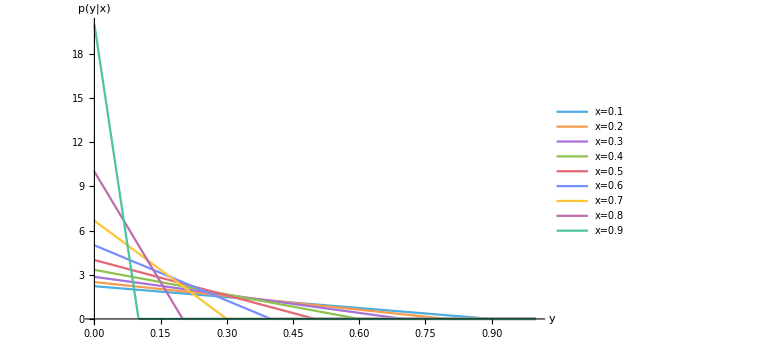

```mathematica
pcond=p[x,y]/p[x]
Plot[Evaluate@Table[pcond/.x->xi,{xi,.1,.9,.1}],{y,0,1},PlotRange->Full,PlotTheme->"PastelColor",AxesLabel->{y,"p(y|x)"},ImageSize->Large,PlotLegends->Table["x="<>ToString[xi],{xi,.1,.9,.1}]]
Export["/home/delon/Dropbox/notes/8.044/assignments/2_3.pdf",%];
```

## Problem 5

```mathematica
$Assumptions=A∈PositiveReals&&η∈PositiveReals&&σ∈PositiveReals
Integrate[A^(3/2)/(σ^2 Sqrt[2 Pi σ^2])1/ξ^(5/2) Exp[-A / (2 σ^2 ξ)],{ξ,A/ η^2,Infinity}]
g=D[%,η]//FullSimplify
```

A∈ℝ&&A>0&&η∈ℝ&&η>0&&σ∈ℝ&&σ>0

-(ⅇ^(-η^2/(2 σ^2)) √(2/π) η)/σ+Erf[η/(√2 σ)]

(ⅇ^(-η^2/(2 σ^2)) √(2/π) η^2)/σ^3

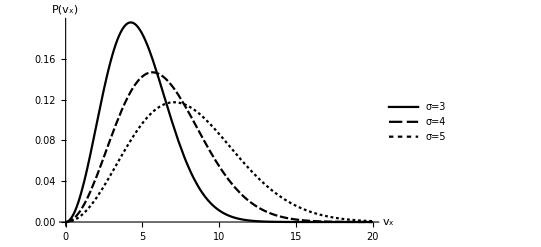

/home/delon/Dropbox/notes/8.044/assignments/2_5.pdf

```mathematica
Plot[Evaluate@Table[g/.σ-> i,{i,3,5}],{η,0,20},PlotTheme->"Monochrome",AxesLabel->{Subscript[v,x],P[Subscript[v,x]]},PlotLegends->Placed[Table["σ="<>ToString[i],{i,3,5}],{Right, Center}]]
Export["/home/delon/Dropbox/notes/8.044/assignments/2_5.pdf",%]
```

## Problem 6

```mathematica
1 - Integrate[Sin[t]/2,{t,ArcSin[rp/R],Pi-ArcSin[rp/R]}]
FullSimplify[D[%,rp],R∈PositiveReals]
```

1-√(1-rp^2/R^2)

rp/(R √((R-rp) (R+rp)))